```mathematica
xMin=-8.; xMax=8.;
sol=NDSolveValue[{
D[u[t,x],t]==6 u[t,x]D[u[t,x],x]-D[u[t,x],{x,3}],
u[0,x]==-2Sech[x]^2, u[t,xMin]==u[t,xMax]},
u,{x,xMin,xMax},{t,-1,1}]
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

InterpolatingFunction[{{-1., 1.}, {…, -8., 8., …}}, <>]

```mathematica
Plot3D[sol[t,x],{x,xMin,xMax},{t,-1,1},PlotRange->All,PlotPoints->40,Mesh->False]
```

-Graphics3D-

```mathematica
xMin=-8.; xMax=8.;n=2.;
sol=NDSolveValue[{
D[u[t,x],t]==6 u[t,x]D[u[t,x],x]-D[u[t,x],{x,3}],
u[0,x]==-n(n+1)Sech[x]^2, u[t,xMin]==u[t,xMax]},
u,{x,xMin,xMax},{t,-1,1}]
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point t == -0.109793.

$Aborted

```mathematica
Plot3D[sol[t,x],{x,xMin,xMax},{t,-1,1},PlotRange->All,PlotPoints->40,Mesh->False]
```

-Graphics3D-

#### Two soliton solution to the KdV

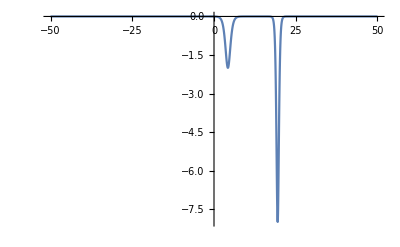

```mathematica
t=1.2;
Plot[ -12(3 + 4 Cosh[2x-8t]+Cosh[4x-64t])/(3Cosh[x-28t]+Cosh[3x-36t])^2,{x,-50,50},PlotRange->All]
```

```mathematica
Manipulate[Plot[ -12(3 + 4 Cosh[2x-8t]+Cosh[4x-64t])/(3Cosh[x-28t]+Cosh[3x-36t])^2,{x,-100,100},PlotRange->All],{t,0,50,0.1}]
```

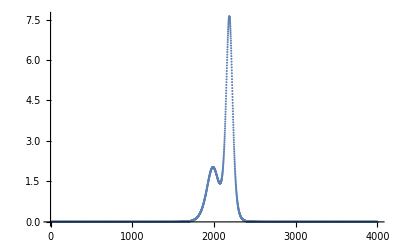

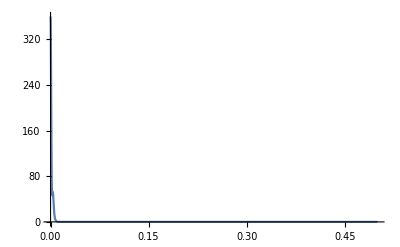

```mathematica
t=0.1;kdv2soliton=Table[12(3 + 4 Cosh[2x-8t]+Cosh[4x-64t])/(3Cosh[x-28t]+Cosh[3x-36t])^2,{x,-20,20,.01}];
ListPlot[kdv2soliton,PlotRange->All]
Periodogram[kdv2soliton,ScalingFunctions->"Absolute",PlotRange->All]
```